```mathematica
myModel[populationSize_,mutationRate_]:=(
(*Set initial condition*)
abFrequency=1; (*frequency of the allele to be followed (A)*)
AbFrequency=0;
aBFrequency=0;
ABFrequency=0;
numberOfGenerations=1000;

(*Initialise list in which we will save the frequencies from every pokolenie*)
abfrequencies=Table[0,{numberOfGenerations}];
Abfrequencies=Table[0,{numberOfGenerations}];
aBfrequencies=Table[0,{numberOfGenerations}];
ABfrequencies=Table[0,{numberOfGenerations}];


For[i=1, i≤ numberOfGenerations, i++,

(*mutation*)
abFrequency=(1-mutationRate)^2*abFrequency+(1-mutationRate)*mutationRate*(AbFrequency+aBFrequency)+mutationRate^2*ABFrequency;
AbFrequency=(1-mutationRate)^2*AbFrequency+(1-mutationRate)*mutationRate*(ABFrequency+abFrequency)+mutationRate^2*aBFrequency;
aBFrequency=(1-mutationRate)^2*aBFrequency+(1-mutationRate)*mutationRate*(ABFrequency+abFrequency)+mutationRate^2*AbFrequency;
ABFrequency=(1-mutationRate)^2*ABFrequency+(1-mutationRate)*mutationRate*(aBFrequency+AbFrequency)+mutationRate^2*abFrequency;

(*selection*)
abw=1;
Abw=1.01;
aBw=1.01;
ABw=1.012;
w=abw*abFrequency+Abw*AbFrequency+aBw*aBFrequency+ABw*ABFrequency;
abFrequency=abFrequency*abw/w;
AbFrequency=AbFrequency*Abw/w;
aBFrequency=aBFrequency*aBw/w;
ABFrequency=ABFrequency*ABw/w;
(*crossing*)
De=abFrequency*ABFrequency-AbFrequency*aBFrequency;

r=0.1;

abFrequency=abFrequency-r*De;
AbFrequency=AbFrequency+r*De;
aBFrequency=aBFrequency+r*De;
ABFrequency=ABFrequency-r*De;

(*sampling*)
abNa=RandomVariate[BinomialDistribution[populationSize,abFrequency]];
abFrequency=abNa/populationSize;
AbNa=RandomVariate[BinomialDistribution[populationSize,AbFrequency]];
AbFrequency=AbNa/populationSize;
aBNa=RandomVariate[BinomialDistribution[populationSize,aBFrequency]];
aBFrequency=aBNa/populationSize;
ABNa=RandomVariate[BinomialDistribution[populationSize,ABFrequency]];
ABFrequency=ABNa/populationSize;

(*saving values*)
abfrequencies[[i]]=abFrequency;
Abfrequencies[[i]]=AbFrequency;
aBfrequencies[[i]]=aBFrequency;
ABfrequencies[[i]]=ABFrequency;

];
Show[
ListPlot[abfrequencies,PlotRange->Automatic,PlotStyle->Gray],
ListPlot[Abfrequencies,PlotRange->Automatic,PlotStyle->Red],
ListPlot[aBfrequencies,PlotRange->Automatic,PlotStyle->Green],
ListPlot[ABfrequencies,PlotRange->Automatic,PlotStyle->Blue]
]
)
```

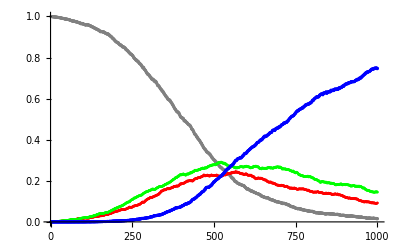

```mathematica
myModel[100000,0.0001]
```